```mathematica
β与α的关系
```

```mathematica
需要先在多个α下计算出相应的β，并保存在文件中
```

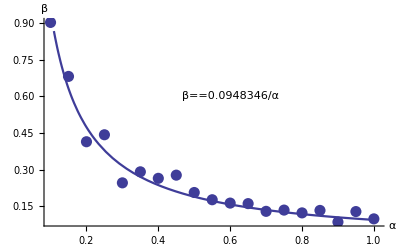

```mathematica
β1=Import["e:/data/fitdata.dat"];
g1=ListPlot[β1,PlotStyle->PointSize[0.02]];
γ=Fit[β1,{1/α},α];
g2=Plot[γ,{α,0.06,1.01},
PlotStyle->Thickness[0.004]];
Show[{g1,g2},
Epilog->{Text[β==γ,{0.6,0.6}]},
AxesLabel->{"α","β"},BaseStyle->{FontSize->13},
AxesStyle->Thickness[0.003]]
Clear[β,γ,α,g1,g2]
```